```mathematica
tremble := {{1-(2p/3),p/3,p/3},{p/3,(1-2p/3),p/3},{p/3,p/3,(1-2p/3)}}
```

```mathematica
matrixIPD := {{R,S,R},{T,P,T/m+P-c/m},{R-c/m, S/m+P(m-1)/m-c/m, R - c/m}}
```

```mathematica
ms := {x,y,z}
y := {y1,y2,y3}
x:= {x1, x2,x3}
```

```mathematica
xp:= tremble.x
yp := tremble.y
```

```mathematica
{(1-p) x+(p y)/2+(p z)/2,(p x)/2+(1-p) y+(p z)/2,(p x)/2+(p y)/2+(1-p) z}
```

{(1-p) x+(p y)/2+(p z)/2,(p x)/2+(1-p) y+(p z)/2,(p x)/2+(p y)/2+(1-p) z}

```mathematica
rp := matrixIPD.yp
rp2 := matrixIPD.xp
```

```mathematica
Reduce[rp[[1]] == rp[[2]] == rp[[3]] && x+y+z==1, {x,y,z}]
```

```mathematica
rp
```

{R ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+S ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+R ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3),(-c/m+P+T/m) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+P ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+T ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3),(-c/m+R) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+(-c/m+((-1+m) P)/m+S/m) ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+(-c/m+R) ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3)}

```mathematica
MSNEcondition = %
```

```mathematica
MSNEforIPD = MSNEcondition /.{T-> 5, R-> 3, P-> 1, S-> 0.1, m-> 10, c-> 0.8}
```

289.98 (-2+3 p)≠0&&x==(0.00344851 (-216.28+289.98 p))/(-2+3 p)&&y==(0.123457 (-1.6+8.1 p))/(-2+3 p)&&z==1-x-y

```mathematica
Eliminate[MSNEforIPD = MSNEcondition /.{T-> 5, R-> 3, P-> 1, S-> 0.1, m-> 10, c-> 0.8},y]
```

43497. x==14499.+1148./(0.666667-1. p)&&43497. z==14499.+5654./(0.666667-1. p)&&-2.+3. p≠0.

```mathematica
Solve[43497. x==14499.+1148./(0.6666666666666666-1. p)&&43497. z==14499.+5654./(0.6666666666666666-1. p)&&-2.+3. p≠0.,{x,z}]
```

{{x→0.0000229901 (14499.+1148./(0.666667-1. p)),z→0.0000229901 (14499.+5654./(0.666667-1. p))}}

```mathematica
FPsolutions =%
```

{{x→0.0000229901 (14499.+1148./(0.666667-1. p)),z→0.0000229901 (14499.+5654./(0.666667-1. p))}}

```mathematica
xb= z+x/2 /.FPsolutions
yb=Sqrt[3]*x/2/.FPsolutions
```

{0.000011495 (14499.+1148./(0.666667-1. p))+0.0000229901 (14499.+5654./(0.666667-1. p))}

{0.00001991 (14499.+1148./(0.666667-1. p))}

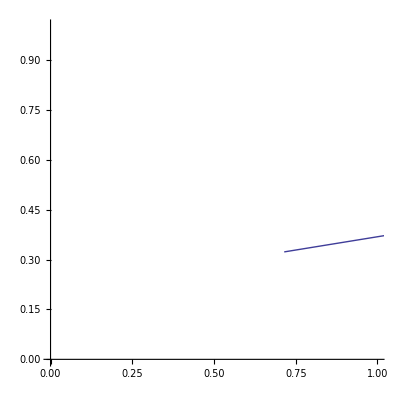

```mathematica
ParametricPlot[{0.000011495045635331173 (14499.+1148./(0.6666666666666666-1. p))+0.000022990091270662345 (14499.+5654./(0.6666666666666666-1. p)),0.000019910003075716454 (14499.+1148./(0.6666666666666666-1. p))},{p,0,0.66}, PlotRange ->{{0,1},{0,1}}]
```

```mathematica
WolframAlpha["x == (0.003448513690599352*(-216.27999999999997 + 289.98*p))/(-2. + 3.*p) && y == (0.12345679012345678*(-1.6 + 8.1*p))/(-2. + 3.*p) && z == 1. + 0.9433754052003586/(-2. + 3.*p) - (2.*p)/(-2. + 3.*p)",{{"LocusSolution",1},"Plaintext"}]
```

3. p-2.!=0.,   x~~(0.0000689703 (14499. p-10814.))/(3. p-2.),   y~~(0.0123457 (81. p-16.))/(3. p-2.),   z~~(0.0000689703 (14499. p-15320.))/(3. p-2.)

```mathematica
i = {1,2,3}
j = {1,2,3}
```

```mathematica
{1,2,3}
g[x_,i_] :=((x[[i]])^(1-a)*Exp[ b*(rp[[i]]) ])/(Sum[x[[j]]^(1-a)*Exp[b*rp[[j]]],{j,3}])
```

{1,2,3}

```mathematica
f[x,i] :=((x[[i]])^(1-a)*Exp[ b*(rp[[i]]) ])/(Sum[x[[j]]^(1-a)*Exp[b*rp[[j]]],{j,3}])
f[y,i] :=((y[[i]])^(1-a)*Exp[ b*(rp2[[i]]) ])/(Sum[y[[j]]^(1-a)*Exp[b*rp2[[j]]],{j,3}])
```

```mathematica
J1 := {D[f[x,i] ,x1], D[f[x,i] ,x2], D[f[x,i], x3]}
```

```mathematica
J1 := Table[ D[f[x,i][[k]], x[[l]]] , {k, 3}, {l, 3}]
```

```mathematica
J2 := Table[ D[f[x,i][[k]], y[[l]]] , {k, 3}, {l, 3}]
```

```mathematica
J3:= Table[ D[f[y,i][[k]], x[[l]]] , {k, 3}, {l, 3}]
J4:= Table[ D[f[y,i][[k]], y[[l]]] , {k, 3}, {l, 3}]
```

```mathematica
J1new :=  Table[J1[[k,l]]-J1[[k,3]], {k,2},{l,2}]
J2new :=Table[J2[[k,l]]-J2[[k,3]], {k,2},{l,2}]
J3new :=Table[J3[[k,l]]-J3[[k,3]], {k,2},{l,2}]
J4new :=Table[J4[[k,l]]-J4[[k,3]], {k,2},{l,2}]
```

```mathematica
J := ArrayFlatten[{{J1new,J2new},{J3new,J4new}}]
```

```mathematica
JIPD := J/. {T-> 5, R-> 3, P-> 1, S-> 0.1, m-> 10, c-> 0.8, p-> 0, x1-> 0.31347276, x2->0.16225831, x3->0.52426893,  y1-> 0.31347276, y2->0.16225831, y3->0.52426893}
```

```mathematica
JI
Eigenvalues[JIPD  /. {a-> 0.001 b-> 0.1}]]
```

$Aborted

0.999457

0.998596

```mathematica
True
```

```mathematica
f[x,i] /.{T-> 5, R-> 3, P-> 1, S-> 0.1, m-> 10, c-> 0.8, p-> 0, x1-> 0.31347276, x2->0.16225831, x3->0.52426893,  y1-> 0.31347276, y2->0.16225831, y3->0.52426893, a-> 0.1, b-> 1}
f[x,i] /.{T-> 5, R-> 3, P-> 1, S-> 0.1, m-> 10, c-> 0.8, p-> 0, x1->0.37292227050141374,x2->0.09876543209876558,x3->0.5283122973998206,y1->0.37292227050141374,y2->0.09876543209876558,y3->0.5283122973998206, a-> 0.1, b-> 1}
```

{0.312938,0.163689,0.523374}

```mathematica
{0.3744392757377952,0.11325812826783734,0.5123025959943673}
fpan[u_, v_,w_] :=f[x,i] /.{T-> 5, R-> 3, P-> 1, S-> 0.1, m-> 10, c-> 0.8, p-> 0, x1->u,x2->v,x3->w,y1->u,y2->v,y3->w, a-> 0.00000001,b-> 0.1}
```

{0.374439,0.113258,0.512303}

```mathematica
~
```

```mathematica
fpan[0.3744392757377952,0.11325812826783734,0.5123025959943673]
```

{(0.374439^(1-(0.→0.1)) ⅇ^(2.67155 b))/(0.374439^(1-(0.→0.1)) ⅇ^(2.67155 b)+0.512303^(1-(0.→0.1)) ⅇ^(2.68329 b)+0.113258^(1-(0.→0.1)) ⅇ^(2.71292 b)),(0.113258^(1-(0.→0.1)) ⅇ^(2.71292 b))/(0.374439^(1-(0.→0.1)) ⅇ^(2.67155 b)+0.512303^(1-(0.→0.1)) ⅇ^(2.68329 b)+0.113258^(1-(0.→0.1)) ⅇ^(2.71292 b)),(0.512303^(1-(0.→0.1)) ⅇ^(2.68329 b))/(0.374439^(1-(0.→0.1)) ⅇ^(2.67155 b)+0.512303^(1-(0.→0.1)) ⅇ^(2.68329 b)+0.113258^(1-(0.→0.1)) ⅇ^(2.71292 b))}

```mathematica
fpan2[u_,v_,w_]:=fpan[fpan[u,v,w][[1]], fpan[u,v,w][[2]], fpan[u,v,w][[3]]] - {u, v, w}
```

```mathematica
fpan2[0.3744392757377952,0.11325812826783734,0.5123025959943673]
```

{-0.000789813,0.000970191,-0.000180377}

```mathematica
{-0.0008045073801519753,0.0006891673805770604,0.00011533999957513696}
```

{-0.000804507,0.000689167,0.00011534}

```mathematica
Plot3D [fpan2[u,v, (1-u-v)], {u, 0, 1}, {v, 0, 1}, PlotPoints-> {20,20}, MaxRecursion -> 0]
```

-Graphics3D-

```mathematica
Plot3D [Norm[fpan2[u,v, (1-u-v)]], {u, 0, 1}, {v, 0, 1}, PlotPoints-> {50,50}, MaxRecursion -> 0]
```

```mathematica
NSolve[fpan2[u, v, w][[1]]==fpan2[u, v, w][[2]]==fpan2[u, v, w][[3]]]
```

{}

```mathematica
xt[x1_,x2_,x3_] := (1-pt)x1 + pt(x2+x3)/2
```

```mathematica
xtf :=xt[xt[x1,x2,x3], xt[x2,x3,x1],xt[x3,x1,x2]]
```

```mathematica
Simplify[xtf]
```

```mathematica
g[x,i]
```

{(ⅇ^(b (R ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+S ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+R ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x1^(1-a))/(ⅇ^(b (R ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+S ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+R ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x1^(1-a)+ⅇ^(b ((-c/m+P+T/m) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+P ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+T ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x2^(1-a)+ⅇ^(b ((-c/m+R) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+(-c/m+((-1+m) P)/m+S/m) ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+(-c/m+R) ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x3^(1-a)),(ⅇ^(b ((-c/m+P+T/m) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+P ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+T ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x2^(1-a))/(ⅇ^(b (R ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+S ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+R ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x1^(1-a)+ⅇ^(b ((-c/m+P+T/m) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+P ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+T ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x2^(1-a)+ⅇ^(b ((-c/m+R) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+(-c/m+((-1+m) P)/m+S/m) ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+(-c/m+R) ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x3^(1-a)),(ⅇ^(b ((-c/m+R) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+(-c/m+((-1+m) P)/m+S/m) ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+(-c/m+R) ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x3^(1-a))/(ⅇ^(b (R ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+S ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+R ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x1^(1-a)+ⅇ^(b ((-c/m+P+T/m) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+P ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+T ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x2^(1-a)+ⅇ^(b ((-c/m+R) ((p y1)/3+(p y2)/3+(1-(2 p)/3) y3)+(-c/m+((-1+m) P)/m+S/m) ((p y1)/3+(1-(2 p)/3) y2+(p y3)/3)+(-c/m+R) ((1-(2 p)/3) y1+(p y2)/3+(p y3)/3))) x3^(1-a))}

```mathematica
x1fp :={0.37292227050141374,0.09876543209876558,0.5283122973998206}
g[x,i]-x/.{T-> 5, R-> 3, P-> 1, S-> 0.1, m-> 10, c-> 0.8, p-> 0, x->x1fp,y->x1fp, a-> 0.00, b-> 1}
```

{-x1+(ⅇ^(3 y1+0.1 y2+3 y3) x1^1.)/(ⅇ^(3 y1+0.1 y2+3 y3) x1^1.+ⅇ^(5 y1+y2+1.42 y3) x2^1.+ⅇ^(2.92 y1+0.83 y2+2.92 y3) x3^1.),-x2+(ⅇ^(5 y1+y2+1.42 y3) x2^1.)/(ⅇ^(3 y1+0.1 y2+3 y3) x1^1.+ⅇ^(5 y1+y2+1.42 y3) x2^1.+ⅇ^(2.92 y1+0.83 y2+2.92 y3) x3^1.),-x3+(ⅇ^(2.92 y1+0.83 y2+2.92 y3) x3^1.)/(ⅇ^(3 y1+0.1 y2+3 y3) x1^1.+ⅇ^(5 y1+y2+1.42 y3) x2^1.+ⅇ^(2.92 y1+0.83 y2+2.92 y3) x3^1.)}

```mathematica
W := {w1,w2,w3}
```

```mathematica
x
```

{x1,x2,x3}

```mathematica
W.x
```

w1 x1+w2 x2+w3 x3

w1*x1 + w2*x2 + w3*x3

$Aborted

```mathematica
mut[k_]:=a(Sum[x[[l]]*Log[x[[l]]], {l,3}] - Log[x[[k]]])
```

```mathematica
mut[1]
```

a (-Log[x1]+x1 Log[x1]+x2 Log[x2]+x3 Log[x3])

```mathematica
mut2:=Sum[x[[l]]*Log[x[[l]]], {l,3}]
```

```mathematica
mut2
```

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification x ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Log[x⟦1⟧] x⟦1⟧+Log[x⟦2⟧] x⟦2⟧+Log[x⟦3⟧] x⟦3⟧

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification x ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Log[x⟦1⟧] x⟦1⟧

```mathematica
Simplify[-Log[x1]+x1 Log[x1]+x2 Log[x2]+x3 Log[x3]]
```

(-1+x1) Log[x1]+x2 Log[x2]+x3 Log[x3]

```mathematica
Exp[mut[1]]
```

ⅇ^(a (-Log[x1]+x1 Log[x1]+x2 Log[x2]+x3 Log[x3]))

```mathematica
Simplify[ⅇ^(a (-Log[x1]+x1 Log[x1]+x2 Log[x2]+x3 Log[x3]))]
```

ⅇ^(a ((-1+x1) Log[x1]+x2 Log[x2]+x3 Log[x3]))

```mathematica
Cancel[ⅇ^(x1 Log[x1]+x2 Log[x2]+x3 Log[x3])/x1]
```

x1^(-1+x1) x2^x2 x3^x3